```mathematica
(* ED results *)
L ={2,4,6,8,10,12,14};

n = {
0.052786404500042045,
0.03877664520080986,
0.034241611576288196,
0.033197838626701615,
0.03296217159120178,
0.032908446302473256,
0.03289605056480251
};

nLSW=0.0776029;
```

0.031365+0.0105543 x+0.0649067 x^2

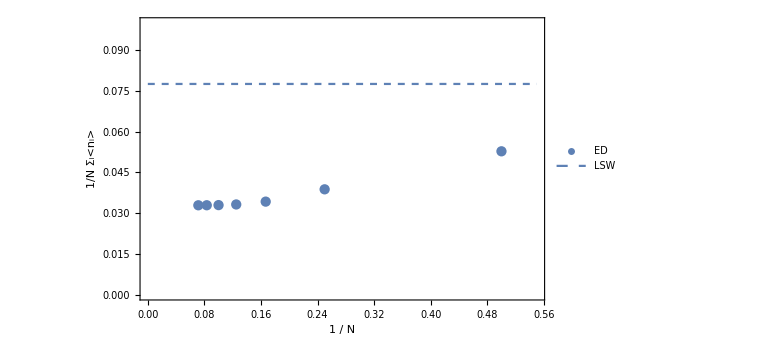

```mathematica
data=Table[{1/L[[it]],n[[it]]},{it,Length[n]}];
fit=Fit[data[[1;;Length[data]]],{1,x,x^2},x]
plt =Show[ListPlot[Legended[data,Placed["ED",{0.9,0.1}]],PlotRange->{{0,0.55},{0,0.1}},Frame->True,ImageSize->Large,FrameLabel->{"1 / N", "1/N Σ_i<n_i>"},FrameStyle->Directive[Black,20]],Plot[Legended[nLSW,Placed["LSW",{0.88,0.18}]],{x,0,0.55},PlotStyle->Dashed]]
```

```mathematica
Table[n[[it]]/n[[it+1]],{it,1,6}]
```

{1.36129,1.13244,1.03144,1.00715,1.00163,1.00038}

```mathematica
SetDirectory["/Users/pwrzosek/Documents/GitHub/XXZ_model/code/mathematica"]
Export["n_scaling.png",plt]
```

/Users/pwrzosek/Documents/GitHub/XXZ_model/code/mathematica

n_scaling.png